# Monte Carlo Method

## Monte Carlo for the Ising model

Consider Ising model on L×L square lattice:

H=-J∑_(<i j>) S_i^z S_j^z

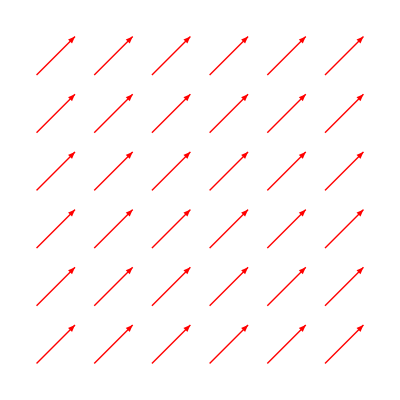

```mathematica
h[x_,y_]:={Polygon[{{0,0}+{x,y},{1,0}+{x,y},{1,1}+{x,y},{0,1}+{x,y}}]};
arrow[x_,y_]:=Arrow[{{-1/3,-1/3}+{x,y},{1/3,1/3}+{x,y}}];
Latt={EdgeForm[Opacity[.7]],White,Table[h[ (i-1),(j-1)],{i,5},{j,5}]};
arrowarray={Red,Table[arrow[ (i-1),(j-1)],{i,6},{j,6}]};
gr={Latt,arrowarray};
Graphics[gr]
```

Generate a trial configuration: select a spin at random, and the trial configuration is the present configuration with the selected spin turned over. The energy difference is given by

Δ E(X→X')=E(X')-E(X)

On the square lattice in two dimension, it is clear that the energy difference depends only on the number of neighbors which have the same spin as the selected spin in the old configuration - between 0 and 4. the energy differences are

(Δ E(X→X') | # of neighbors have the same spin
-8J | 0
-4J | 1
0 | 2
4J | 3
8J | 4)

The trial state is accepted with probability exp[-β Δ E(X→X')] if Δ E(X→X')>0; however, the accepted probability is 1if Δ E(X→X')<0.Since exp[-β Δ E(X→X')] can assume only five different values, it is advisable to store these in an array in order to avoid calculating the exponential function over and over again.

Remark: The initial configuration will be chosen either random or as FM (all spins either + or -). The specific heat is calculated according to

C_V=1/(k_B T^2)(∂^2 Log[Z])/(∂β^2)
=1/(k_B T^2)[(∑_X ⅇ^(-βℋ(X))ℋ^2(X))/(∑_X ⅇ^(-βℋ(X)))-((∑_X ⅇ^(-βℋ(X))ℋ(X))/(∑_X ⅇ^(-βℋ(X))))^2]
=1/(k_B T^2)[⟨E^2⟩_NVT-⟨E⟩_NVT^2]

Similarly, the magnetic susceptibility can be written as

χ=(∂⟨M⟩)/(∂H)=β[⟨M^2⟩-⟨M⟩^2]

## Variational Monte Carlo (VMC)

Variational method:

Construct the trial many-particle wave function ψ_α(R), depending on the S variational parameters α=(α_1,…,α_S). ψ_α depends on the combined position coordinate R of all the N particles R=r_1,…,r_N.

⟨E⟩=ψ_αHψ_α/ψ_αψ_α

Evaluate the expectation value of the energy.

Vary the parameters α according to some minimisation algorithm and return to step 1.

It turns out that in realistic systems the many-body wave function assumes very small values in large parts of configuration space, so a straightforward procedure using homogeneous distributed random points in configuration space is bound to fail. This suggests that it might be efficient to use a Metropolis algorithm in which a collection of random walkers is pushed towards those regions of configuration space where the wave function assumes appreciable values. For any trial wave function ψ_T, the expectation value of the energy can be written as

⟨E⟩=(∫ⅆR ψ_T(R)H ψ_T(R))/(∫ⅆR ψ_T^2(R))=(∫ⅆR ψ_T^2(R)(H ψ_T(R))/(ψ_T(R)))/(∫ⅆR ψ_T^2(R))=(∫ⅆR ψ_T^2(R)E_L(R))/(∫ⅆR ψ_T^2(R))

where we defined the local energy as

E_L(R)=(H ψ_T(R))/(ψ_T(R))

We need to construct a Metropolis-walk in the same spirit as in ordinary Monte Carlo, but now with a stationary distribution ρ(R) given by

ρ(R)=(ψ_T^2(R))/(∫ⅆ R'ψ_T^2(R'))

The procedure is as follows:

Put N walkers at random positions;

REPEAT

Select next walker;

Shift that walker to a new position

Calculate p=(ψ_T^2(R'))/(ψ_T^2(R)), where R' is the new and R is the old configuration

If p<1 the new position is accepted with probability p;

If p≥1 the new position is accepted;

UNTIL finished.

### Harmonic Oscillator

## Diffusion Monte Carlo (DMC)

## Path-Integral Monte Carlo (PMC)

## Determinant Quantum Monte Carlo methods

Consider Hubbard model

Ĥ=-t∑_(i,j,σ) c_σ^†(i)c_σ(j)+U∑_i n_↑(i)n_↓(i)-μ∑_(i, σ) n_σ(i)

For any observable, Ô, we are concerned about its expectation value, defined as

⟨Ô⟩=(Tr Ô ⅇ^(-β Ĥ))/(Tr ⅇ^(-β Ĥ))

The trace is summation over all possible states, which is impossible in practice. However, we can choose important states to find the average by Monte Carlo sampling rather than running over all possible states. In this case we have

⟨Ô⟩=(∑_c p[c]O[c])/(∑_c p[c])

where p[c] is the probability of the configuration c to have the value of O[c]. The configurations {c}=c_1,c_2… are successively generated from a Markov-chain process via a proper description on the transition probability W(c_i→c_(i+1)), called important sampling. As already been pointed out, the Metropolis algorithm satisfies the detailed balance principle. In the classical systems, we use the Boltzmann distribution p[c]=ⅇ^(-β E[c]). When probability ratio p[c']/p[c]>1 we accept the new configuration c' whereas when p[c']/p[c]<1 we still allow certain obability to determine whether accept or reject updating from c to c'.

However, for quantum systems, E[c] is very difficult to evaluate as we have to diagonalize the full Hamiltonian in Hilbert space. From path integral, the partition function is given as

Z=Tr[(ⅇ^(-Δτ Ĥ))^M]=Tr[(∏_(l=1))^M ⅇ^(-Δτ (Ĥ)_l)]=Tr[(∏_(l=1))^M ⅇ^(-Δτ ((Ĥ)_l^t+(Ĥ)_l^U))]

By applying the first and second order Suzuki-Trotter decomposition, the partition function can be, respectively, written as

Z=Tr[(∏_(l=1))^M ⅇ^(-Δτ (Ĥ)_l^t)ⅇ^(-Δτ (Ĥ)_l^U)]+O((Δτ)^2 t U)

Z=Tr[(∏_(l=1))^M ⅇ^(-Δτ ((Ĥ)_l^t)/2)ⅇ^(-Δτ (Ĥ)_l^U)ⅇ^(-Δτ ((Ĥ)_l^t)/2)]+O((Δτ)^3 t U)

In the former one, the noninteracting part are evolution kernel

ⅇ^(-Δτ (Ĥ)_l^t)=ⅇ^(-Δτ ∑_(i,j,σ) c_σ^†(i)K_(i j)^σ c_σ(j))

where for Hubbard model K_(i j)^σ=-t for i and j connected by a bond. The interaction term

Un_↑(i)n_↓(i)=-U/2{[n_↑(i)-n_↓(i)]^2-[n_↑(i)+n_↓(i)]^2}

can be decomposed by a discrete Hubbard-Stratonovich transformation (Hirsch, Fye). For U>0, we have

ⅇ^(-Δτ Un_↑(i)n_↓(i))=1/2∑_(s_l=±1) ∏_(σ=↑,↓) ⅇ^(-(σ s_l(i)λ+(U Δτ)/2)n_σ(i))

where

λ=cosh^-1(ⅇ^(U/2 Δτ))

The partition function could be rewritten as

Z=Tr[(∏_(l=1))^M ⅇ^(-Δτ (Ĥ)_l^t)ⅇ^(-Δτ (Ĥ)_l^U)]
=Tr[(∏_(l=1))^M ⅇ^(-Δτ ∑_(i,j,σ) c_σ^†(i)K_(i j)^σ c_σ(j))(∏_(l=1))^M(∏_(i=1))^N 1/2∑_(s_l=±1) ∏_(σ=↑,↓) ⅇ^(-(σ s_l(i)λ+(U Δτ)/2-Δτ μ)n_σ(i))]
=(1/2)^(N M)Tr[(∏_(l=1))^M ⅇ^(-Δτ ∑_(i,j,σ) c_σ^†(i)K_(i j)^σ c_σ(j))(∏_(i=1))^N(∏_(l=1))^M∑_(s_l=±1) ∏_(σ=↑,↓) ⅇ^(-(σ s_l(i)λ+(U Δτ)/2-Δτ μ)n_σ(i))]
=(1/2)^(N M)Tr[(∏_(l=1))^M ⅇ^(-Δτ ∑_(i,j,σ) c_σ^†(i)K_(i j)^σ c_σ(j))∑_{s} (∏_(l=1))^M(∏_(i=1))^N∏_(σ=↑,↓) ⅇ^(-(σ s_l(i)λ+(U Δτ)/2-Δτ μ)n_σ(i))]
=(1/2)^(N M)Tr[∑_{s} ∏_(σ=↑,↓) (∏_(l=1))^M ⅇ^(-Δτ ∑_(i,j) c_σ^†(i)K_(i j)^σ c_σ(j))ⅇ^(-∑_i (σ s_l(i)λ+(U Δτ)/2-Δτ μ)n_σ(i))]
=(1/2)^(N M)∑_{s} Tr[∏_(σ=↑,↓) (∏_(l=1))^M ⅇ^(-Δτ ∑_(i,j) c_σ^†(i)K_(i j)^σ c_σ(j))ⅇ^(-∑_i (σ s_l(i)λ+(U Δτ)/2-Δτ μ)n_σ(i))]
=(1/2)^(N M)∑_{s} det[1+B_M^↑… B_1^↑]det[1+B_M^↓… B_1^↓]
=(1/2)^(N M)∑_{s} ∏_(σ=↑,↓) det O^σ({s})

where

B_l^σ=ⅇ^(-Δτ K^σ)ⅇ^(V_l^σ),V_l^σ(i)=-(σ s_l(i)λ+(U Δτ)/2-Δτ μ)

O^σ({s})=1+B_M^σ… B_1^σ

obviously, we have

p[c]=∏_(σ=↑,↓) det O^σ({s})

as the probability for Ising-spin configuration {s} in the Metropolis algorithm. If at l-th time step a spin at site i is flipped, s_l(i)→s_l(i)'=-s_l(i), then the corresponding single-particle propagator becomes (B_l^σ)' and the probability ratio is

R[c';c]=p[c']/p[c]=∏_(σ=↑,↓) det[1+B_M^σ…(B_l^σ)'… B_1^σ]/det[1+B_M^σ… B_l^σ… B_1^σ]

The evaluation of probability ratio is tedious. But it turns out R[c';c] can be simplified as

det[1+B_M^σ…(B_l^σ)'… B_1^σ]/det[1+B_M^σ… B_l^σ… B_1^σ]=1+(1-[G_l^σ]_(i i))(ⅇ^(2λ σs_l(i))-1)

where

[G_l^σ]_(i j)=⟨c_σ(i)c_σ^†(j)⟩

which can be calculated as follows:

[G_l^σ]_(i j)=⟨c_σ(i)c_σ^†(j)⟩_{s}=(Tr c_σ(i)c_σ^†(j)ⅇ^(-β Ĥ))/(Tr ⅇ^(-β Ĥ))

Notice that the subscript {s} denotes that the Green’s function is given with the Hubbard Stratonovich field configuration. Unlike classical systems, once a spin is flipped, we have to update the Green’s function under new HS Ising spin configuration {s'}. It can be shown that

[G_l^σ]_(i j)=[(1+B_(l-1)^σ… B_1^σ B_M^σ… B_l^σ)^-1]_(i j)

The updated Green’s function can be derived as

[G_l^σ]_(j k)→([G_l^σ]')_(j k)=[(1+B_(l-1)^σ… B_1^σ B_M^σ… (B_l^σ)')^-1]_(j k)

=[G_l^σ]_(j k)-({δ_(j i)-[G_l^σ]_(j i)}(γ_l^σ(i)[G_l^σ])_(i k))/(1+{1-[G_l^σ]_(i i)}γ_l^σ(i))

where γ_l^σ(i)=ⅇ^(2λ σ s_l(i))-1. After a complete lattice sweep, the random walk has to time evolve to the next time step, from the l-th to (l+1)-th, then G_(l+1)^σ can be prepared as

G_(l+1)^σ=B_l^σ(G_l^σ(B_l^σ))^-1

However, this step cannot guarantee the accuracy after few time evolution steps; in particular for large β. To make calculations numerically stable, we need to recalculate G_l^σ by using Eq. (DisplayFormulaNumbered) again.